```mathematica
G[x_] =Exp[-x^2/2]/Sqrt[2*Pi]
```

(ⅇ^(-x^2/2))/(√(2 π))

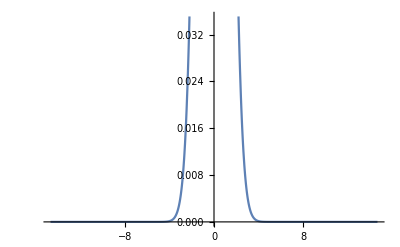

```mathematica
Plot[(ⅇ^(-x^2/2))/(√(2 π)),{x,-14.696938456699069,14.696938456699069}]
```

```mathematica
Plot[G[x]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[G[x]]

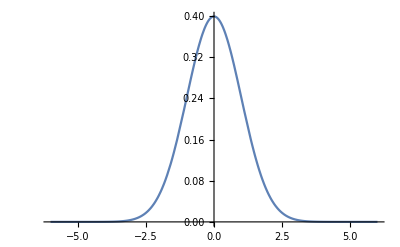

```mathematica
Plot[G[x],{x,-6,6}]
```

```mathematica
L[x]=1\Sqrt[2*Pi]*1\(x^4+1)
```

```mathematica
Plot[L[x],{x,-6,6}]
```

-Graphics-

```mathematica
L[x]=(0.5*x^4+1)^(-1)
```

1/(1+0.5 x^4)

```mathematica
Plot[G[x],L[x]/Sqrt[2*Pi],{x,-6,6}]
```

Plot::nonopt: Options expected (instead of {x,-6,6}) beyond position 2 in Plot[G[x],L[x]/(√(2 π)),{x,-6,6}]. An option must be a rule or a list of rules.

Plot[G[x],L[x]/(√(2 π)),{x,-6,6}]

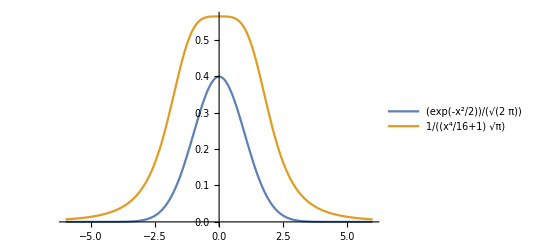

```mathematica
Plot[{Exp[-x^2/2]/Sqrt[2*Pi] ,(1/16*x^4+1)^(-1)/Sqrt[Pi]},{x,-6,6},PlotLegends->"Expressions"]
```

```mathematica
FindRoot[Exp[-x^2/2]/Sqrt[2*Pi]-(0.5*x^4+1)^(-1)/Sqrt[Pi],{x,10}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{x→4.90943×10^10}

```mathematica
G[10]
```

```mathematica
G[10]
```

G[10]

```mathematica
Integrate[(0.5*x^4+1)^(-1)/Sqrt[Pi],x]
```

1.12838 (0.210224 ArcTan[0.594604 (-1.68179+2. x)]+0.210224 ArcTan[0.594604 (1.68179+2. x)]-0.105112 Log[1.41421-1.68179 x+1. x^2]+0.105112 Log[1.41421+1.68179 x+1. x^2])

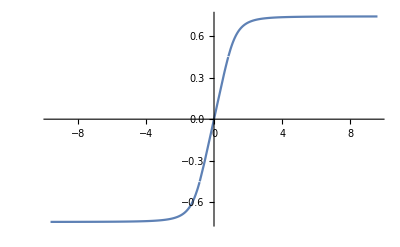

```mathematica
Plot[%38,{x,-9.5880692106139,9.5880692106139}]
```